# Neural activity

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
cd=ColorData[97,"ColorList"];
```

```mathematica
dir ="../AnalysisData/best_categ_pass_agent/";
(*dir = "../AnalysisData/best_offset/";*)
```

## Random NN

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
a=Import["nn.dat"];
```

```mathematica
b = Transpose[Take[a,{2000,25000,100},{1,100}]];
```

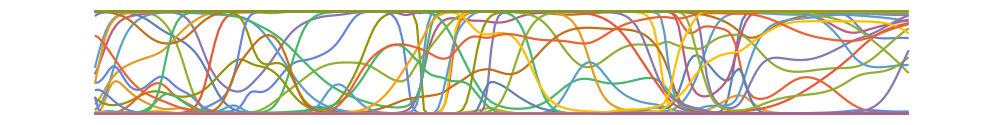

randomneuralactivity.eps

```mathematica
ListLinePlot[b,Frame->False,Axes->False,FrameTicks->False,AspectRatio->1/8,ImageSize->1000]
Export["randomneuralactivity.eps",%]
```

## Task 1: Object Categorization

```mathematica
ba1=Import[StringJoin[dir,"B_avoid_n1.dat"]];
ba2=Import[StringJoin[dir,"B_avoid_n2.dat"]];
ba3=Import[StringJoin[dir,"B_avoid_n3.dat"]];
ba4=Import[StringJoin[dir,"B_avoid_n4.dat"]];
ba5=Import[StringJoin[dir,"B_avoid_n5.dat"]];
bc1=Import[StringJoin[dir,"B_catch_n1.dat"]];
bc2=Import[StringJoin[dir,"B_catch_n2.dat"]];
bc3=Import[StringJoin[dir,"B_catch_n3.dat"]];
bc4=Import[StringJoin[dir,"B_catch_n4.dat"]];
bc5=Import[StringJoin[dir,"B_catch_n5.dat"]];
```

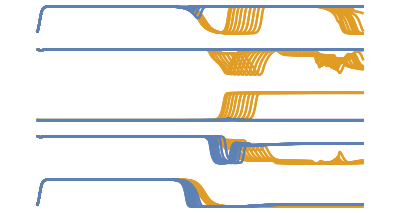

ObjectRecog.eps

```mathematica
GraphicsColumn[
{
Show[{
ListLinePlot[bc1,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba1,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc2,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba2,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc3,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba3,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc4,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba4,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[bc5,PlotStyle->cd[[2]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[ba5,PlotStyle->cd[[1]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
Export["ObjectRecog.eps",%]
```

## Task 2: Perceiving affordances

```mathematica
aa1=Import[StringJoin[dir,"A_avoid_n1.dat"]];
aa2=Import[StringJoin[dir,"A_avoid_n2.dat"]];
aa3=Import[StringJoin[dir,"A_avoid_n3.dat"]];
aa4=Import[StringJoin[dir,"A_avoid_n4.dat"]];
aa5=Import[StringJoin[dir,"A_avoid_n5.dat"]];
ac1=Import[StringJoin[dir,"A_pass_n1.dat"]];
ac2=Import[StringJoin[dir,"A_pass_n2.dat"]];
ac3=Import[StringJoin[dir,"A_pass_n3.dat"]];
ac4=Import[StringJoin[dir,"A_pass_n4.dat"]];
ac5=Import[StringJoin[dir,"A_pass_n5.dat"]];
```

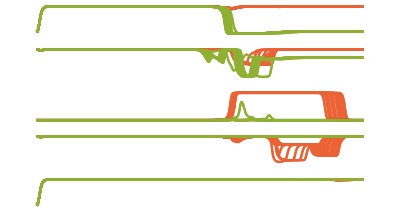

PercAff.eps

```mathematica
GraphicsColumn[
{
Show[{
ListLinePlot[ac1,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aa1,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[ac2,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aa2,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[ac3,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aa3,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[ac4,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aa4,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}],
Show[{
ListLinePlot[ac5,PlotStyle->cd[[4]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700],
ListLinePlot[aa5,PlotStyle->cd[[3]],PlotRange->{Automatic,{-0.1,1.1}},Axes->False,Frame->False,AspectRatio->1/10,ImageSize->700]
}]
}
]
Export["PercAff.eps",%]
```